```mathematica
$packageDir = "~/Documents/IDrive-Sync/Work/Delft/Projects/Purification/Simulations/QSIM"
```

~/Documents/IDrive-Sync/Work/Delft/Projects/Purification/Simulations/QSIM

```mathematica
$Packages
```

{QSIM`errorAnalysis`,QSIM`nonlocal`,QSIM`superoperators`,QSIM`noise`,QSIM`stabilizers`,QSIM`measurement`,QSIM`basicfunctions`,GetFEKernelInit`,StreamingLoader`,IconizeLoader`,CloudObjectLoader`,ResourceLocator`,PacletManager`,System`,Global`}

```mathematica
Needs["QSIM`basicfunctions`",FileNameJoin[{$packageDir,"QSIM_basicFunctions.m"}]]
Needs["QSIM`measurement`",FileNameJoin[{$packageDir,"QSIM_measurement.m"}]]
Needs["QSIM`stabilizers`",FileNameJoin[{$packageDir,"QSIM_stabilizers.m"}]]
Needs["QSIM`nonlocal`",FileNameJoin[{$packageDir,"QSIM_nonlocal.m"}]]
Needs["QSIM`noise`",FileNameJoin[{$packageDir,"QSIM_noise.m"}]]
Needs["QSIM`superoperators`",FileNameJoin[{$packageDir,"QSIM_superoperators.m"}]]
Needs["QSIM`errorAnalysis`",FileNameJoin[{$packageDir,"QSIM_errorAnalysis.m"}]]
```

Parameters that define the raw state (generated by a single photon click): 

vis - the visibility of the photons
fz  - determined by initialization error, MW pulse infidelity and spin flip probability  
r  - the proportion of the state in the unentangled ‘11’ state

The r value depends on: 

pd - the probability that a photon emitted is detected pd = pZPL*pDetect where: 
	- pZPL - probability that a given photon is in the zero photon line
	- pDetect - detection efficiency
theta  - the initial rotation of the state of the qubits: Cos[theta]|0> + Sin[theta]|1>

(or can treat the raw state as being werner state in which case we need only the fidelity: 
fid - The fidelity of the raw state immediately after it is generated if there was no photon loss) 

NOTE THAT IN THIS FILE, 0 IS THE DARK STATE

pDC - probability of a dark count (so that actually in 0, even though think in one)


The parameters of the distillation procedure:

pCNOT - the error rate when a CNOT gate can be performed between electron and nuclear qubits
pSWAP - the error rate when a SWAP operation is performed between electron and nuclear qubits
pmBright - the probability of error in measuring the bright state
pmDark - the probability of error in measuring the dark state
pp - the probability for a phase error between the generation of raw state 1 & 2

-----------------------------------------------
	Additional parameters
-----------------------------------------------
pCarbonDephasing - the probability for a phase error on the stored carbon state
RndOpticalPhase - the phase imprinted on the first raw state (this parameter is only just to check the robustness of the protocol

the function rawState[fid_,pLoss_] generates a density matrix of the entangled state generated after a single detector click

```mathematica
rValue[theta_,pZPL_,pDetect_,pDC_]:=Module[{p00,p01,p11,pd},
pd = pZPL*pDetect;
p00 = 2*Cos[theta]^4*pDC*(1-pDC); (* detected a dark count, but state is actually 0 *)
p01 = 2(Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd+ 2*pDC*(1-pDC)*(1-pd)); (*detected the actual signal, or lost signal photon, but detected a dark count*)
p11 = Sin[theta]^4 *((1-pDC)^2*2*(pZPL*pDetect*(1-pDetect)) + 2(1-pDC)*pDC*(1-pd)^2); (*no dark count, detect one, but dont detect the other + dont detect either photon, do detect a dark count. *)

{p00,p01,p11}/(p00+p01+p11)
]

rValueWithoutZPLpostselect[theta_,pZPL_,pDetect_,pDC_]:=Module[{p00,p01,p11,pd},
pd = pZPL*pDetect;
p00 = 2*Cos[theta]^4*pDC*(1-pDC);
p01 = 2(Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd+ 2*pDC*(2-pDC)*(1-pd));
p11= Sin[theta]^4 *((1-pDC)^2*2*pd(1-pd) + 2(1-pDC)*pDC*(1-pd)^2);

{p00,p01,p11}/(p00+p01+p11)
]

(*There is a cost to the rate of the protocol from adjusting theta. *)
RelativeRate[theta_,pDC_,pZPL_,pDetect_]:=Module[{pd,p00,p01,p11},
pd = pZPL*pDetect;
p00 = 2*Cos[theta]^4*pDC*(1-pDC); (* detected a dark count, but state is actually 0 *)
p01 = 2(Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd+ 2*pDC*(1-pDC)*(1-pd)); (*detected the actual signal, or lost signal photon, but detected a dark count*)
p11 = Sin[theta]^4 *((1-pDC)^2*2*(pZPL*pDetect*(1-pDetect)) + 2(1-pDC)*pDC*(1-pd)^2); (*no dark count, detect one, but dont detect the other + dont detect either photon, do detect a dark count. *)
{p00,p01,p11}
]
```

### r value with and without postselection on the non-zpl photons

The larger theta is, the higher the probability of being in 11 when detecting one photon (a bad thing):

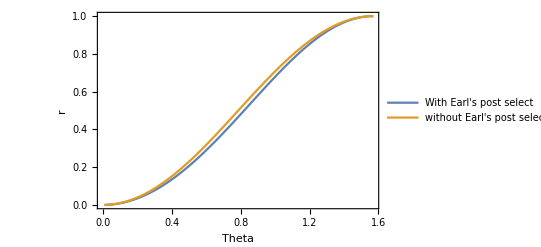

```mathematica
thetaRange = Range[0.01,Pi/2,0.01];
ListPlot[{
Thread[{thetaRange,rValue[#,0.03,0.13,0.00][[3]]&/@thetaRange}],
Thread[{thetaRange,rValueWithoutZPLpostselect[#,0.03,0.13,0.00][[3]]&/@thetaRange}]},
Joined->True,
Frame->True,
FrameLabel->{"Theta","r"},
PlotLegends->{"With Earl's post select","without Earl's post select"}]
```

Note that with dark counts, you don’t want too small a theta, since then the chance of actually producing a real photon is comparable to the dark count rate. However, shifting to smaller theta means that less likely to be in the one one state - there is a balance between the two effects:

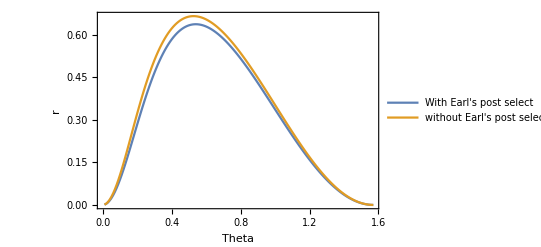

```mathematica
thetaRange = Range[0.01,Pi/2,0.01];
ListPlot[{
Thread[{thetaRange,rValue[#,0.03,0.13,0.0005][[2]]&/@thetaRange}],
Thread[{thetaRange,rValueWithoutZPLpostselect[#,0.03,0.13,0.0005][[2]]&/@thetaRange}]},
Joined->True,
Frame->True,
FrameLabel->{"Theta","r"},
PlotLegends->{"With Earl's post select","without Earl's post select"}]
```

### Raw state generation

For the p01 component of the classical mixture, the density matrix is:

1-fz | 0 | 0 | 0
0 | fz | -ⅇ^(ⅈ RndOpticalPhase) vis | 0
0 | -ⅇ^(-ⅈ RndOpticalPhase) vis | fz | 0
0 | 0 | 0 | 1-fz

For the p00 and p11 components, they are just 00 and 11 product states respectively.

NOTE that now have switched zero and one states. In previous, one is the state that excites. Now zero is the state that excites

```mathematica
rawState [vis_,fz_,rValue_,RndOpticalPhase_]:=Chop[rValue[[1]]*KP[zero,zero]+rValue[[2]]*0.5*{{1-fz,0,0,0},{0,fz,-vis*Exp[ⅈ*RndOpticalPhase],0},{0,-vis*Exp[-ⅈ*RndOpticalPhase],fz,0},{0,0,0,1-fz}}+rValue[[3]]*KP[one,one]];
```

```mathematica
rawState[0.9,0.99,{0,0.5,0.5},0.5π]//MatrixForm
```

(0.0025 | 0 | 0 | 0
0 | 0.2475 | 0.-0.225 ⅈ | 0
0 | 0.+0.225 ⅈ | 0.2475 | 0
0 | 0 | 0 | 0.5025)

### EPL protocol

```mathematica
eplFromRawState[inputState_,pCNOT_,pSWAP_,pmDark_,pmBright_,pp_,pCarbonDephasing_]:=Module[{rawState,rawState1,rawState2,state,cz1,cz2,hads,p,swap1,swap2},

rawState = inputState;
(*the state gets swapped onto nuclear spins *)
state = KP[rawState,zero,zero];
swap1 = twoQgate[4,1,3,swap];
swap2 = twoQgate[4,2,4,swap];
state = swap1.state.CT[swap1];
state = swap2.state.CT[swap2];
state = applyGateNoise[state,pSWAP,1,3];
state = applyGateNoise[state,pSWAP,2,4];

(*the electron spins are measured out in the zero state: NB this is post selective *)
rawState1 = measureOutcomeReal[state,{0,0},pmDark]; (* PH NOTE Calculate probability of failure here? *)

(* generate another raw pair on the electrons, this time there's some phase shift pp from the first one *)
rawState2 = (1-pp)*rawState + pp*KP[pZ,id].rawState.KP[pZ,id];

(*dephasing of the stored state is modelled symmetrically for both nuclear spins*)
rawState1 = (1-pCarbonDephasing)^2*rawState1 + pCarbonDephasing*(1-pCarbonDephasing)*KP[pZ,id].rawState1.KP[pZ,id]+pCarbonDephasing*(1-pCarbonDephasing)*KP[id,pZ].rawState1.KP[id,pZ]+pCarbonDephasing^2*KP[pZ,pZ].rawState1.KP[pZ,pZ];

state=KP[rawState1,rawState2];

cz1=twoQgate[4,1,3,cnotB];
cz2=twoQgate[4,2,4,cnotB];

state=cz1.state.CT[cz1];
state=cz2.state.CT[cz2];

state=applyGateNoise[state,pCNOT,1,3];
state=applyGateNoise[state,pCNOT,2,4];

state=measureOutcomeReal[state,{1,1},pmDark]; (* PH NOTE Calculate probability of failure here? *)

state= KP[pX,id].state.KP[pX,id];


Chop[state/Tr[state]]


]
```

```mathematica
eplRotatedFromRawState[inputState_,pCNOT_,pSWAP_,pmDark_,pmBright_,pp_,pCarbonDephasing_]:=Module[{rawState,rawState1,rawState2,state,cz1,cz2,hads,p,swap1,swap2},

rawState = inputState;
(*the state gets swapped onto nuclear spins *)
rootX = MatrixExp[-ⅈ*pX*π/4]; 
state = KP[rawState,zero,zero];
swap1 = twoQgate[4,1,3,swap];
swap2 = twoQgate[4,2,4,swap];
state = swap1.state.CT[swap1];
state = swap2.state.CT[swap2];
state = applyGateNoise[state,pSWAP,1,3];
state = applyGateNoise[state,pSWAP,2,4];

(*the electron spins are measured out in the zero state: NB this is post selective *)
rawState1 = measureOutcomeReal[state,{0,0},pmDark];
rawState1 = KP[rootX,rootX].rawState1.KP[rootX†,rootX†]; (* PH NOTE This occurrs with unit fidelity. Consider this. *)

(* generate another raw pair on the electrons, this time there's some phase shift pp from the first one *)
rawState2 = (1-pp)*rawState + pp*KP[pZ,id].rawState.KP[pZ,id];

(*dephasing of the stored state is modelled symmetrically for both nuclear spins*)
rawState1 = (1-pCarbonDephasing)^2*rawState1 + pCarbonDephasing*(1-pCarbonDephasing)*KP[pZ,id].rawState1.KP[pZ,id]+pCarbonDephasing*(1-pCarbonDephasing)*KP[id,pZ].rawState1.KP[id,pZ]+pCarbonDephasing^2*KP[pZ,pZ].rawState1.KP[pZ,pZ];

rawState1 = KP[rootX†,rootX†].rawState1.KP[rootX,rootX];
state=KP[rawState1,rawState2];

cz1=twoQgate[4,1,3,cnotB];
cz2=twoQgate[4,2,4,cnotB];

state=cz1.state.CT[cz1];
state=cz2.state.CT[cz2];

state=applyGateNoise[state,pCNOT,1,3];
state=applyGateNoise[state,pCNOT,2,4];

state=measureOutcomeReal[state,{1,1},pmDark];


state= KP[pX,id].state.KP[pX,id];

Chop[state/Tr[state]]
]
```

```mathematica
outputState[theta_,pZPL_,pDetect_,pDC_,vis_,fz_,pCNOT_,pSWAP_,pmDark_,pmBright_,pp_,pCarbonDephasing_,RndOpticalPhase_]:=Module[{rawstate,rval},

rval=rValue[theta,pZPL,pDetect,pDC];

rawstate = rawState[vis,fz,rval,RndOpticalPhase];

eplFromRawState[rawstate,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing]
]
```

```mathematica
outputStateRotated[theta_,pZPL_,pDetect_,pDC_,vis_,fz_,pCNOT_,pSWAP_,pmDark_,pmBright_,pp_,pCarbonDephasing_,RndOpticalPhase_]:=Module[{rawstate,rval},

rval=rValue[theta,pZPL,pDetect,pDC];

rawstate = rawState[vis,fz,rval,RndOpticalPhase];

eplRotatedFromRawState[rawstate,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing]
]
```

## Calculate output fidelity

```mathematica
Module[{pCNOT,pSWAP,pmDark,pmBright,pp,vis,fz,theta,pZPL,pDetect,pDC,pCarbonDephasing,RndOpticalPhase},

pCNOT=0.025;
pSWAP = 0.05;
pmDark = 0.01;
pmBright = 0.1;
pp = 0.01;
pCarbonDephasing = 0.05;
RndOpticalPhase = 0.5π;

vis = 0.95;
fz = 0.99;

theta =0.5*Pi/3;
pZPL = 0.03;
pDetect = 0.13;
pDC=10^-7;

{Re@Fidelity[outputState[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase],bellState[0]],Re@Fidelity[outputStateRotated[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase],bellState[0]]}
]
```

{0.807395,0.842091}

## Output fidelity dependence on error parameters

```mathematica
plotParameter[param_]:=Module[{pCNOT,pSWAP,pmDark,pmBright,pp,vis,fz,theta,pZPL,pDetect,pDC,pCarbonDephasing,CDephasingRange,thetaRange,fidelities,fidelitiesRot,outputsRot,pSWAPrange,gaterange,fidelityRange,pDetectRange,darkcountrange,RndOpticalPhase,RndOpticalPhaseRange,range,outputs,default,def},

pCNOT=0.025;
pSWAP = 0.05;
pmDark = 0.01;
pmBright = 0.1;
pp = 0.01;
vis = 0.95;
fz = 0.99;
theta =0.5*Pi/3;
pZPL = 0.03;
pDetect = 0.13;
pDC=10^-7;
pCarbonDephasing = 0.05;
RndOpticalPhase = 0.5π;


thetaRange=Range[0.01,Pi/2,0.01];
gaterange = Range[0,0.1,0.002];
fidelityRange = Range[0.7,1,0.01];
pDetectRange=Range[0,0.2,0.001];
darkcountrange = Range[10^-7,0.01,0.0002];
CDephasingRange = Range[0,0.5,0.01];
RndOpticalPhaseRange = Range[0,2π,0.05];


default=Fidelity[bellState[0],outputState[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]];

If[param=="theta",range = thetaRange; def =theta;
outputs =  outputState[#,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[#,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="pCNOT", range = gaterange; def = pCNOT;
outputs =  outputState[theta,pZPL,pDetect,pDC,vis,fz,#,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,pDetect,pDC,vis,fz,#,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="pSWAP",range = gaterange; def = pSWAP;
outputs =  outputState[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,#,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,#,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="pZPL",range = pDetectRange; def = pZPL;
outputs =  outputState[theta,#,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,#,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="pDetect",range = pDetectRange; def = pDetect;
outputs =  outputState[theta,pZPL,#,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,#,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="pDC",range = darkcountrange; def = pDC;
outputs =  outputState[theta,pZPL,pDetect,#,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,pDetect,#,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="vis",range = fidelityRange; def = vis;
outputs =  outputState[theta,pZPL,pDetect,pDC,#,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,pDetect,pDC,#,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="fz",range = fidelityRange; def = fz;
outputs =  outputState[theta,pZPL,pDetect,pDC,vis,#,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,pDetect,pDC,vis,#,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="pmDark",range = gaterange; def = pmDark;
outputs =  outputState[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,#,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,#,pmBright,pp,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="pmBright",range = gaterange;def = pmBright;
outputs =  outputState[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,#,pp,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,#,pp,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="pp",range = gaterange; def = pp;
outputs =  outputState[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,#,pCarbonDephasing,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,#,pCarbonDephasing,RndOpticalPhase]&/@range;];
If[param=="pCarbonDephasing",range = CDephasingRange; def = pCarbonDephasing;
outputs =  outputState[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,#,RndOpticalPhase]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,#,RndOpticalPhase]&/@range;];
If[param=="RndOpticalPhase",range = RndOpticalPhaseRange; def = RndOpticalPhase;
outputs =  outputState[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,#]&/@range;
outputsRot =  outputStateRotated[theta,pZPL,pDetect,pDC,vis,fz,pCNOT,pSWAP,pmDark,pmBright,pp,pCarbonDephasing,#]&/@range;];


fidelities=Re@Fidelity[#,bellState[0]]&/@outputs;
fidelitiesRot = Re@Fidelity[#,bellState[0]]&/@outputsRot;
pltRange= {Min[Join[fidelities,fidelitiesRot]]-0.01,Max[Join[fidelities,fidelitiesRot]]+0.01};
Show[
ListPlot[Thread[{range,fidelities}],Joined->True,Frame->True,FrameLabel->{param,"output fidelity"},PlotRange-> pltRange],
ListPlot[Thread[{range,fidelitiesRot}],Joined->True,Frame->True,PlotStyle->Red,PlotRange-> pltRange],
ListPlot[{{def,Re[default]}},PlotMarkers-> {"◆", 18}]
]

]
```

### Plotting output fidelity over each parameter

The function takes a default set of values (as defined in the function above) and varies the specified parameter to determine the output fidelity in blue (Addendum: and the output fidelity of the EPL protocol with rotated Basis in red.). The diamond shows the point of the default values. For example:

### Optimising theta

Calling the function on theta we can see how the fidelity increases as theta is reduced (i.e. a greater fraction of the initial state is in ‘0’). The effect falls off at small theta when dark counts become important.

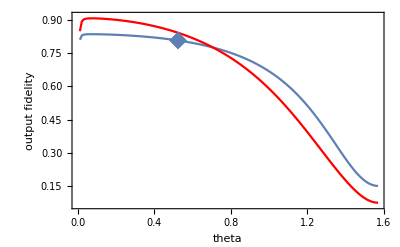

```mathematica
plotParameter["theta"]
```

Note that this comes at a cost in the relative rate of the protocol giving a click (from the desired process):

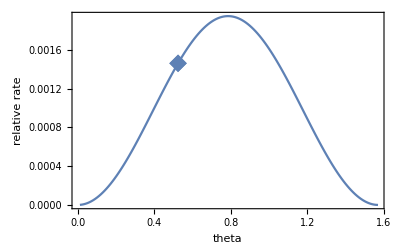

```mathematica
relativeRatePlot[] :=Module[{theta,pZPL,pDetect,pDC,thetaRange,rates},
theta =0.5*Pi/3;
pZPL = 0.03;
pDetect = 0.13;
pDC=10^-7;
thetaRange=Range[0.01,Pi/2,0.01];

rates =  RelativeRate[#,pDC,pZPL,pDetect][[2]]&/@thetaRange;
Show[
ListPlot[Thread[{thetaRange,rates}],Joined->True,Frame->True,FrameLabel->{"theta","relative rate"}],
ListPlot[{{theta,RelativeRate[theta,pDC,pZPL,pDetect][[2]]}},PlotMarkers-> {"◆", 18}]
]
]
relativeRatePlot[]
```

### pDarkCount (I suppose this is the probability to detect a DC within our detection window: that is roughly 10^-7)

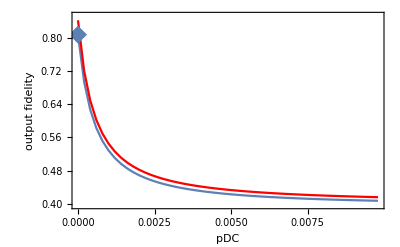

```mathematica
plotParameter["pDC"]
```

### Dephasing of the stored state

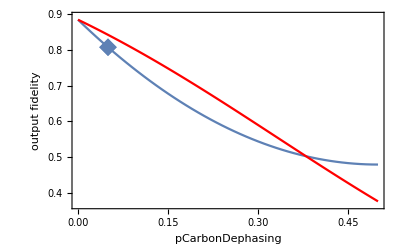

```mathematica
plotParameter["pCarbonDephasing"] (*This graph is taken for an internal phase of 0.5π (this is the worst case for storing in a rotated basis.) I guess this is the most important graph of this notebook. Storing in a rotated basis is superior for a large range of dephasing probabilities.*)
```

### Random internal phase on the generated entangled state

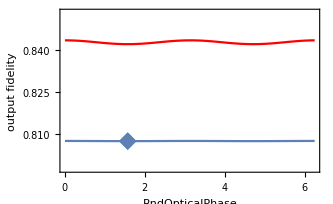

```mathematica
plotParameter["RndOpticalPhase"]
```

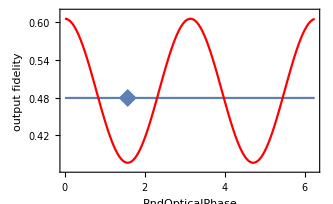
```mathematica
(*I obtained this graph by setting pCarbonDephasing = 0.5 as default value in plotParameter.*)
(*I.e. the stored state is completely dephased and only ZZ correlations remain.
The output fidelity when storing in the rotated basis (red line) starts to depend on the internal phase of the raw state leading to an overall mixed state.*)
-Graphics-
```

-Graphics-